Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 2. Crittografia

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 2.1 (Decrittazione di messaggio (Hill)).

### Testo dell’esercizio

Il messaggio

"WWMGuuuqkYUFwYcWV'.YryomxpQvkfmzaqqpKQEtUpWKES.ZArynoXGDqrymGOeQEvkfmzaqqpKQEtUpWKEtCuoXPqqYxiqZAKEaDocjVKseHV' WPtCTC'.KKzxranoXGDqKEuuWWcQXPxGpKfvxGEVKEtzJyaDTUxGEV' sCeExwNbrvkluKEuuGG' alAhqraryhqKEuuGGLXcYncCCgapQncDqyouq; aXGOqkkGGgaGfOl; IJyaDqWqWrymGOeQE; aXGOqkk' alAhqraM.wTTRWkuuMGuuGGMGqqTUsgfRJyITUFOqqqWnTXqTtwwNTXncCCpyKETXryo UFKErjkkgLLmwT'' xvncqmyomxpQOqqqWnTXryqqpyQEVtqT; UEbxvkkWnTXuuTUvkfmzaqqpKQErynoXGDqyoYoBFvklutUv' kkIZJyKErjkkgLdS`mevQEFlKK.`kI; U.lhRUtaD"

è stato prima codificato in una lista di numeri, poi crittato con Hill ed infine decodificato e ritrasformato in una stringa. La codifica/decodifica iniziale e finale utilizza i seguenti codici numerici per i seguenti 58 caratteri, che includono tutte le lettere minuscole e maiuscole e altri sei caratteri:

Carattere | ASCII | Codice usato
A, …, Z | 65, …, 90 | 1, …, 26 (ASCII - 64)
a, …, z | 97, …, 122 | 33, …, 58 (ASCII - 64)
. | 46 | 27
, | 44 | 28
spazio | 32 | 29
` | 96 | 30
' | 39 | 31
; | 59 | 32

La crittazione alla Hill è stata fatta usando una matrice intera 2×2 invertibile in ℤ_58. Ci sono circa 12 milioni di tali matrici (scritte a coefficienti in ℤ_58) e di esse oltre 4 milioni  sono invertibili in ℤ_58. Questo è un numero troppo alto per provare a decrittare il messaggio con tutte. Però si sa che il messaggio è stato crittato usando una matrice invertibile in ℤ_58 il cui determinante è congruo a 1 (mod 58) e ci sono “solo” 146160 tali matrici.

### Svolgimento

Innanzitutto assegniamo il messaggio ad una variabile.

```mathematica
messaggio="WWMGuuuqkYUFwYcWV'. YryomxpQvkfmzaqqpKQEtUpWKES.ZArynoXGDqrymGOeQEvkfmzaqqpKQEtUpWKEtCuoXPqqYxiqZAKEaDocjVKseHV'WPtCTC'.KKzxranoXGDqKEuuWWcQXPxGpKfvxGEVKEtzJyaDTUxGEV'sCeExwNbrvkluKEuuGG'alAhqraryhqKEuuGGLXcYncCCgapQncDqyouq;aXGOqkkGGgaGfOl;IJyaDqWqWrymGOeQE;aXGOqkk'alAhqraM.wTTRWkuuMGuuGGMGqqTUsgfRJyITUFOqqqWnTXqTtwwNTXncCCpyKETXryo UFKErjkkgLLmwT''xvncqmyomxpQOqqqWnTXryqqpyQEVtqT;UEbxvkkWnTXuuTUvkfmzaqqpKQErynoXGDqyoYoBFvklutUv'kkIZJyKErjkkgLdS`mevQEFlKK.`kI;U.lhRUtaD";
```

Controlliamo, poi, che la stringa ricevuta abbia un numero pari di caratteri, così da rendere più agevole la decrittazione in seguito.

```mathematica
StringLength@messaggio//EvenQ
```

Creiamo una funzione che converta le stringhe nel sistema a cinquantotto caratteri richiesto. Benché non sia necessariamente l’approccio più elegante, decidiamo di sottrarre 64 dal codice ASCII di tutti i caratteri e di aggiustare con regole di sostituzione adeguate i caratteri non alfabetici.

```mathematica
stringaAdNumeri[str_]:=(
ToCharacterCode[str]-64
)/.{
46-64->27,(*punto*)
44-64->28,(*virgola*)
32-64->29,(*spazio*)
96-64->30,(*accento grave*)
39-64->31,(*apostrofo / accento acuto*)
59-64->32 (*punto e virgola*)
}
```

Analogamente, ne scriviamo anche la funzione inversa. Poiché le regole di sostituzione sono formalmente espressioni del tipo Rule[expr1, expr2], usiamo Reverse per non doverle riscrivere a rovescio manualmente.

```mathematica
numeriAdStringa[l_]:=FromCharacterCode[
(
(
l/.Reverse/@{
46-64->27,(*punto*)
44-64->28,(*virgola*)
32-64->29,(*spazio*)
96-64->30,(*accento grave*)
39-64->31,(*apostrofo / accento acuto*)
59-64->32 (*punto e virgola*)
}
)/.{0->58}(*z*)
)+64
]
```

Scriviamo una funzione che divida in coppie la lista di numeri creata dalla trasformazione da stringhe a numeri. Non dobbiamo preoccuparci di gestire il caso in cui la stringa abbia un numero dispari di caratteri, perché messaggio è di lunghezza pari.

```mathematica
coppie[l_]:=Partition[l,2]
```

```mathematica
mes0=messaggio//stringaAdNumeri//coppie;
```

Generiamo tutte le matrici di ℤ_58 ed estraiamo quelle di determinante congrue a 1 mod 58: per le proprietà del determinante, infatti, il fatto che la chiave privata abbia determinante congruo 1 mod 58 implica che anche la sua inversa abbia determinante congruo a 1 mod 58.

```mathematica
chiavi=Select[Tuples[Range[0,57],{2,2}],Det[#,Modulus->58]==1&];
```

Effettivamente ci sono 146160 chiavi.

```mathematica
Length@chiavi
```

Creata una funzione di sostegno per applicare la matrice a tutte le coppie di una lista, generiamo tutte le possibili decrittazioni.

```mathematica
scalare[matrice_,lista_]:=matrice.#&/@lista
```

```mathematica
possibili=Flatten/@Mod[Map[scalare[#,mes0]&,chiavi],58];
```

Le decrittazioni possibili sono troppe per poterle controllare manualmente: occorre, dunque, un criterio con cui controllarne solo una piccola parte. Cominciamo visualizzando la quantità di lettere minuscole presenti nelle decrittazioni possibili. Per vedere il numero esatto di casi per ogni barra, è sufficiente porre la freccia del mouse sopra tale barra.

Histogram[Count[#, a_ /; 33 <= a <= 58] & /@ possibili]

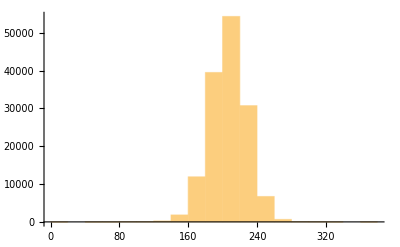

Come si può notare mettendo la freccia del mouse a ridosso dell’asse x, ci sono davvero poche stringhe che abbiano più di 300 caratteri minuscoli. Un primo apporccio, quindi, può consistere nel controllare le stringhe in base a quanti caratteri minuscoli contengono. Controlliamo se la stringa con più caratteri minuscoli è quella giusta.

```mathematica
massimo=Max[Count[#,a_/;33≤a≤58]&/@possibili];
sequenza=Select[possibili,Count[#,a_/;33≤a≤58]==massimo&]//First;
```

sequenza // numeriAdStringa (*Dà il messaggio in chiaro.*)

Dal momento che questo approccio ha restituito una frase di senso compiuto, ora troviamo la matrice che è stata usata per decrittare il messaggio ed invertiamola, in modo da ottenere la chiave privata usata inizialmente.

```mathematica
posizione=Position[possibili,sequenza]⟦1,1⟧;
Inverse[chiavi⟦posizione⟧,Modulus->58]
```

Se questo approccio non avesse funzionato, avremmo potuto scartare progressivamente le stringhe usando, nell’ordine, i seguenti criterii:

rimuovere le stringhe con una frequenza troppo alta di lettere maiuscole: come si vede nel grafico, infatti, sono poche le stringhe con un numero di lettere maiuscole non eccessivo;

Histogram[Count[#, a_ /; 1 <= a <= 26] & /@ possibili]

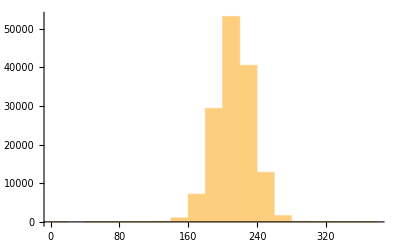

rimuovere le stringhe che iniziano con un segno di punteggiatura (a parte l’accento grave, che può anche essere usato per aprire le virgolette) o con uno spazio;

rimuovere le stringhe che contengono sottosequenze prive di senso, come ad esempio due virgole o le virgolette aperte e subito richiuse;

rimuovere le stringhe in cui compaiono sottostringhe con una lettera minuscola seguita da una maiuscola senza altri segni in mezzo.

Quest’ultimo criterio, sensato in lingua italiana, perde di utilità in inglese, nella cui lingua esistono nomi propri “ben formati” con una lettera minuscola subito prima di una maiuscola.

## Esercizio 2.2 (RSA).

### Testo dell’esercizio

Determinare, usando le capacità simboliche di Mathematica, un’espressione della chiave privata b in funzione di m, p, q e a.

Scrivere una funzione che crei in modo random le chiavi pubbliche (m, a) e private (m, b) per RSA; a può essere “poco random”, per esempio molto piccolo: la segretezza del sistema dipende dalla difficoltà di determinare b.

Provare a generare delle chiavi RSA che siano “Mathematicamente sicure”: m è così grande che Mathematica non riesce a fattorizzarlo in un tempo ragionevole.

Se non riuscite a generare così dei primi p e q abbastanza grandi, cercateli su libri o in Internet; per esempio, si possono usare primorial primes oppure, perché no?, Padovan primes.

Dopo aver creato le vostre chiavi RSA personali (m, a, b), usatele per inviare la soluzione dell’esercizio precedente: crittate la stringa decrittata con le vostre chiavi private e con le chiavi pubbliche del docente. Non dimenticate di indicare nel notebook le vostre chiavi pubbliche!

Attenzione. L’ordine in cui applicare le crittazioni con le chiavi (m, b) e (m', a') non è indifferente: dipende da quale sia maggiore tra m e m'.

### Svolgimento

Creiamo innanzitutto un’espressione per b dati p, q e a.

```mathematica
keyb[p_,q_,a_]:=PowerMod[a,-1,(p-1)(q-1)]
```

Se vogliamo avere un’espressione per b dati solo m e a, allora occorre prima fattorizzare m e poi applicare l’identità (p-1)(q-1)=m-p-q-1

```mathematica
keyb2[m_,a_]:=Module[{p,q},
{p,q}=First/@FactorInteger[m];(*Assumiamo come precondizione che m = p q per opportuni primi p, q*)
keyb[p,q,a](*ovvero PowerMod[a, -1, m - p - q - 1]*)
]
```

Per creare casualmente le chiavi RSA, risulta conveniente usare un modulo, così da localizzare la creazione dei primi p e q. Abbiamo deciso di implementare la funzione di modo che possiamo scegliere se inserire manualmente due numeri primi scelti prima oppure se lasciare a Mathematica la loro creazione. Abbiamo deciso di fornire una chiave pubblica a casuale e prima.

```mathematica
mab[k_]:=Module[(*Funzione per generare casualmente le chiavi*)
{p,q,m,a,b,primecheck,coprimecheck},
(
primecheck[{p1_,q1_}]:=If[
And[p1≠q1,PrimeQ[p1],PrimeQ[q1]],
{p1,q1},
Prime@RandomInteger[{10^k,10^(k+2)},2]
];
{p,q}=FixedPoint[primecheck,{0,0}];
coprimecheck[p2_,q2_][n_]:=If[CoprimeQ[n,(p2-1)(q2-1)],n,Prime@RandomInteger[{10^Floor[k/2],10^(Floor[k/2]+2)}]];
a=FixedPoint[coprimecheck[p,q],0];
m=p q;
b=keyb[p,q,a];
ClearAll[p,q];(*In questo modo, si elimina ogni possibilità di conoscere i primi p, q generati casualmente*)
{m,a,b}
)
]
mab[p0_,q0_,k_]:=If[(*Funzione che richiede due numeri primi espliciti*)
And[p0≠q0,PrimeQ[p0],PrimeQ[q0]],
Module[
{coprimecheck,a},
coprimecheck[p2_,q2_][n_]:=If[CoprimeQ[n,(p2-1)(q2-1)],n,Prime@RandomInteger[{10^Floor[k/2],10^(Floor[k/2]+2)}]];
a=FixedPoint[coprimecheck[p0,q0],0];
{p0 q0,a,keyb[p0,q0,a]}
],
mab[k]
]
```

Come intuibile dalla documentazione, la creazione di chiavi è legata a k in modo esponenziale, perché esponenziale è la complessità computazionale di Prime.

ListPlot[Union@Flatten[Table[Table[{k, Timing[mab[k] // First] // First}, 10], {k, 5, 12}], 1]]

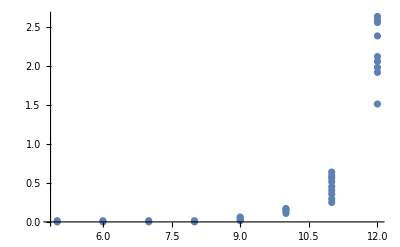

A ciò, però, non corrisponde un aumento così evidente di complessità computazionale per la fattorizzazione.

Module[
 {lista = Union@Flatten[Table[Table[{k, First@mab[k]}, 50], {k, 5, 12}], 1]},
 ListPlot[
  Table[{x[[1]], First@Timing[FactorInteger[x[[2]]]]}, {x, lista}], PlotRange -> All
  ]
 ]

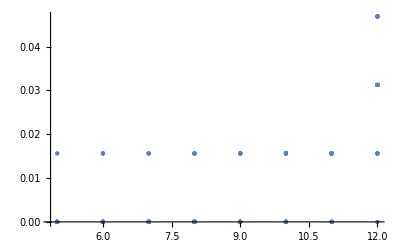

Volendo usare come chiavi RSA qualcosa di più “Mathematicamente sicuro”, abbiamo utilizzato numeri primi trovati su https://bigprimes.org. Riportiamo in basso le nostre chiavi pubbliche.

```mathematica
m=134730867248747143322781722117343687452495402440369304273009;
a=164573911;
```

Timing[FactorInteger[m]] // First (*Out[·] = 46.78125 sul nostro computer*)

Poiché la fattorizzazione di questo m non è immediata, benché lungi dallo scoraggiare un possibile attacco di “uomo al mezzo”, decidiamo di mantenerlo.

Creiamo delle funzioni che utilizzino la cifratura RSA per codificare il messaggio.

```mathematica
listRSA[aprime_,mprime_,b_,m_]:= PowerMod[PowerMod[#,aprime,mprime],b,m]&
rsaCrypt1[aprime_,mprime_,b_,m_,msg_]:= listRSA[b,m,aprime,mprime]@ToCharacterCode[msg]
rsaDecrypt1[bprime_,mprime_,a_,m_,lst_]:= FromCharacterCode[listRSA[a,m,bprime,mprime]@lst]

rsaCrypt[aprime_,mprime_,b_,m_,msg_]:= If[mprime>m,rsaCrypt1[aprime,mprime,b,m,msg],rsaCrypt1[b,m,aprime,mprime,msg]]
rsaDecrypt[bprime_,mprime_,a_,m_,lst_]:=If[mprime>m,rsaDecrypt1[bprime,mprime,a,m,lst],rsaDecrypt1[a,m,bprime,mprime,lst]]
```

Abbiamo automatizzato il processo di modo che crittazione e decrittazione vengano eseguite nell’ordine corretto, ossia crittando prima con l’m minore e poi col maggiore tra i due. Inoltre includiamo le chiavi pubbliche del professore.

```mathematica
mprime=32396927179105460035141194885599771540108841915199866657593871814632213862698727791094102157;
aprime=25917541743284368028112955908479816141682631584427030752119054761164747747860237097951508301;
```

Usando le funzioni sopra, forniamo già crittato il messaggio dell’Esercizio 2.1; nel commento è contenuto il comando con cui l’abbiamo generato, che presume che b sia noto. Per visualizzare la lista completa, è sufficiente fare click sul tasto + e poi su Uniconise.

```mathematica
messaggionascosto=(*rsaCrypt[aprime, mprime, b, m, messaggiotrovato]*);
```

```mathematica
rsaDecrypt[bprime,mprime,a,m,messaggionascosto]
```

## Esercizio 2.3 (Un algoritmo di hashing).

### Testo dell’esercizio

Si completino i dettagli di un algoritmo appena descritto, spiegando tutte le scelte fatte.

Lo si implementi in Mathematica.

Si illustri con alcuni esempi il fatto che piccole variazioni nel dato in ingresso producono grandi variazioni dell’hash. Se questo non avviene, provare a modificare la funzione f scelta al passo 2. Se volete, potete anche confrontare funzioni costruite con diverse scelte — ma non è obbligatorio.

### Svolgimento

La funzione di hash che proponiamo segue il seguente algoritmo:

prende la stringa di cui calcolare l’hash e la converte in una lista di blocchi di 32 elementi ciascuno, aggiungendo eventualmente l’equivalente degli spazi per raggiungere tale forma; poiché il codice ASCII dello spazio è 32, l’aggiunta di spazi alla fine di un blocco aumenta la dimensione dell’hash abbastanza da mascherare eventuali similarità di hash tra due stringhe simili;

eleva alla sedicesima il primo elemento di ogni sottolista: ciò previene che stringhe molto corte abbiano un’hash che inizia in modo simile e che liste corte che contengono gli stessi caratteri abbiano la stessa hash;

perché tutti i numeri delle varie liste siano dispari, applica ad ognuno di essi la funzione f(n)=2n+1; in questo modo è comunque rispettato il requisito che tutti i numeri debbano essere minori di 256;

a partire dal primo blocco, calcola il prodotto di tutti i numeri all’interno di essa e moltiplica questo risultato per 1, nella prima sottolista, oppure per il prodotto creato precedentemente, per tutte le altre;

esaurite le ripetizioni del passaggio precedente, mostra il risultato in base 16.

```mathematica
hash[str_]:=BaseForm[
Fold[
Mod[#1 Times@@#2,2^256]&,
1,
2(
#/.{{i_,j__}->{i^16,j}}&/@
Partition[
PadRight[
ToCharacterCode[str],
StringLength[str]+Mod[32-StringLength[str],
32],
32],
32](*Questa ricorrenza del 32, benché curiosa, non è voluta.*)
)+1
],
16
]
```

Questa funzione di hash restituisce risultati assai diversi anche per stringhe molto simili: non ci sono particolari ricorrenze se viene aggiunto un singolo carattere

```mathematica
hash["Nel mezzo del cammin di nostra vita"]
hash["Nel mezzo del cammin di nostra vita,"]
```

o se un carattere è sostituito, anche col suo successivo.

```mathematica
hash["Nel mezzo del cammin di nostra vita"](*Cambiamo l'ultimo carattere*)
hash["Nel mezzo del cammin di nostra vitb"]
```

```mathematica
hash["Nel mezzo del cammin di nostra vita"](*Cambiamo il primo carattere*)
hash["Mel mezzo del cammin di nostra vita"]
```

```mathematica
hash["Nel mezzo del cammin di nostra vita"](*Cambiamo il secondo carattere*)
hash["Nfl mezzo del cammin di nostra vita"]
```

```mathematica
hash["Nel mezzo del cammin di nostra vita"](*Cambiamo un carattere nel mezzo della frase*)
hash["Nel mezzo del canmin di nostra vita"]
```

Quest’ultima differenza è ottenuta anche su stringhe molto corte, ovvero di uno o due caratteri, grazie all’elevamento alla sedicesima: senza tale passaggio, infatti, stringhe di un singolo carattere avrebbero un’hash che inizia in modo molto simile, in quanto il risultato della moltiplicazione differirebbe “poco” rispetto all’ordine di grandezza dell’hash stessa.

```mathematica
hash[FromCharacterCode[0]]
hash[FromCharacterCode[1]]
```

```mathematica
hash["1"]
hash["2"]
```

L’uso dei pattern per realizzare questa modifica è stata l’unica soluzione considerata che non prevedesse la creazione di una funzione ausiliaria e che risultasse leggibile.